# Péndulo simple

## Lagrangiano

```mathematica
EulerLagrange[L_,q_]:=Block[{lhs,rhs},
lhs = D[D[L,q'[t]],t];
rhs = D[L,q[t]];
Solve[lhs==rhs,q''[t]]
];
```

```mathematica
L = 1/2 m l^2 θ'[t]^2- m g l (1-Cos[θ[t]]);
```

```mathematica
EulerLagrange[L,θ]
```

{{θ''[t]→-(g Sin[θ[t]])/l}}

## Solución numérica

```mathematica
sol = With[{m=1,l= 1,g=9.8},
First@NDSolve[{θ''[t]+g/l Sin[θ[t]]==0,θ[0]== π/3,θ'[0]==0},θ,{t,0,10}]
]
```

{θ→InterpolatingFunction[…]}

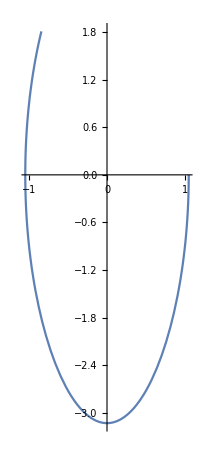

```mathematica
ParametricPlot[{θ[t],θ'[t]}/.sol,{t,0,1.3}]
```

## Gráfica del Lagrangiano

```mathematica
Clear[L]
```

```mathematica
firstPoint = {θ[0],θ'[0]}/.sol;
lastPoint = {θ[1.3],θ'[1.3]}/.sol;
```

```mathematica
L[{θ_,θp_}]:=Block[{m = 1,l = 1,g = 9.81},1/2 m l^2 θp^2- m g l (1-Cos[θ])];
```

```mathematica
LAtFirst = L[firstPoint];
LAtLast = L[lastPoint];
```

```mathematica
Show[
Plot3D[
L[{θ,θp}],{θ,-2π,2π},{θp,-2π,2π},
ColorFunction->Function[{x,y,z},Hue[z]]
],
ListPointPlot3D[
{Append[firstPoint,LAtFirst+0.02],Append[lastPoint,LAtLast+0.02]},
PlotStyle->{Red,PointSize[0.02]}
]
]
```

-Graphics3D-

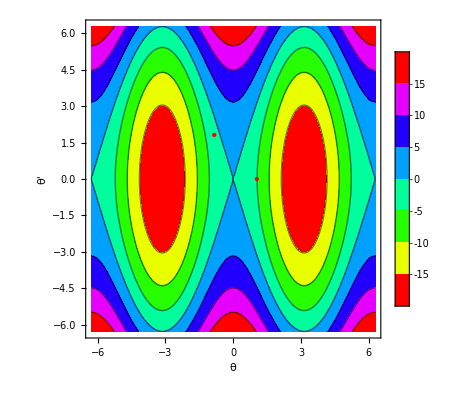

```mathematica
Show[
ContourPlot[
L[{θ,θp}],{θ,-2π,2π},{θp,-2π,2π},
FrameLabel->{"θ","θ'"},
ColorFunction->Hue,
PlotLegends->Automatic
],
ListPlot[{firstPoint,lastPoint},PlotStyle->{Red,PointSize[Large]}]
]
```

### Curvas de Bezier

```mathematica
DynamicModule[{r},
Manipulate[
r = BezierFunction[lo];
ParametricPlot[
r[tp],{tp,0,1},Epilog->{Black,Line[lo]},PlotRange->{{-2π,2π},{-2π,2π}}
]
,
{{lo,pts},Locator},
Initialization:>(pts={firstPoint,{0.5,-1},{-0.5,0.5},lastPoint}),
TrackedSymbols:>{lo}
]
]
```

### Integral sobre curva de Bezier

```mathematica
DynamicModule[{r},
Manipulate[
r = BezierFunction[lo];

Show[
ContourPlot[
L[{θ,θp}],{θ,-2π,2π},{θp,-2π,2π},
FrameLabel->{"θ","θ'"},
ColorFunction->Hue,
PlotLegends->Automatic,
PlotLabel->"L(θ,θ') = "<>ToString[NIntegrate[Evaluate[L[r[tp]]],{tp,0,1}]]
],
ParametricPlot[
r[tp],{tp,0,1},Epilog->{Black,Line[lo]},PlotRange->{{-2π,2π},{-2π,2π}}
]
]
,
{{lo,pts},Locator},
Initialization:>(pts={firstPoint,{0.5,-1},{-0.5,0.5},lastPoint}),
TrackedSymbols:>{lo}
]
]
```

### Curva de Bezier vs trayectoria real

```mathematica
DynamicModule[{r},
Manipulate[
r = BezierFunction[lo];

Show[
ContourPlot[
L[{θ,θp}],{θ,-2π,2π},{θp,-3π,3π},
FrameLabel->{"θ","θ'"},
ColorFunction->Hue,
PlotLegends->Automatic,
PlotLabel->"L(θ,θ') = "<>ToString[NIntegrate[Evaluate[L[r[tp]]],{tp,0,1}]]
],
ParametricPlot[
r[tp],{tp,0,1},Epilog->{Black,Line[lo]},PlotRange->{{-2π,2π},{-2π,2π}}
],
ParametricPlot[{θ[t],θ'[t]}/.sol,{t,0,1.3},PlotStyle->Orange]
]
,
{{lo,pts},Locator},
Initialization:>(pts={firstPoint,{0.5,-1},{-0.5,0.5},lastPoint}),
TrackedSymbols:>{lo}
]
]
```